Radiation pressure + back-action evasion for nondegenerate internal squeezing

Attempt 1: Using Hamiltonian from Li et al, 2020

```mathematica
(*setting global assumptions*)
$Assumptions={Ω≥0,γa≥0,γbtot≥γR>0,γc≥0,1>Rpd≥0,χ≥0,ωs>0,β∈Reals,ρRP≥0,ρBAE≥0,αOG∈Reals,ϕ∈Reals};
(*where β=(αGW Larm)/(2^(1/2)ℏ), ρRP=ρBAE=αGW^2/(2^(1/2)ℏ μ);*)

Id=IdentityMatrix[2];
(*simplifying upstream to better the end result*)
Ma=(γa-ⅈ Ω)Id+(ⅈ ρRP)/(2^(1/2)Ω^2)({{1, 1}, {-1, -1}});
invMa=Inverse[Ma]//Simplify;
Mc=(γc-ⅈ Ω)Id-(ⅈ ρBAE)/(2^(1/2)Ω^2)({{1, 1}, {-1, -1}});
invMc=Inverse[Mc]//Simplify;
Mb=(γbtot-ⅈ Ω)Id+ωs^2 Inverse[Ma]-χ^2({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}}).Inverse[Mc].({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}});(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
TimeConstraint0={0.1,1};
invMb=Simplify[Inverse[Mb],TimeConstraint->TimeConstraint0];

Γ=1/2^(1/2)({{1, 1}, {-ⅈ, ⅈ}});
Rin=Simplify[((1-Rpd)^(1/2)Γ.(Id-2 γR invMb).Inverse[Γ]),TimeConstraint->TimeConstraint0];
Rb=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)(2 (γbtot-γR))^(1/2)Γ. invMb.Inverse[Γ]),TimeConstraint->TimeConstraint0];
Ra=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)ωs (2 γa)^(1/2)Γ. invMb.invMa.Inverse[Γ]),TimeConstraint->TimeConstraint0];
Rc=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)(-χ)(2 γc)^(1/2)Γ.invMb.({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}}).invMc.Inverse[Γ]),TimeConstraint->TimeConstraint0];(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
T=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)ωs (-ⅈ β)Γ. invMb.invMa.({{1, 0}, {0, -1}})),TimeConstraint->TimeConstraint0];

Sx=Simplify[(
Rpd Id
+Rin.ConjugateTranspose[Rin]
+Ra.ConjugateTranspose[Ra]
+Rb.ConjugateTranspose[Rb]
+Rc.ConjugateTranspose[Rc]),TimeConstraint->{1,5}];
(*signal transfer function is Subscript[X, PD,2] wrt h not (X⃗)_PD wrt h⃗ --> factor of two from Subscript[(T.({{1}, {1}})), 22] versus Subscript[T, 22]
NB: another subtlety in that Subscript[T, 21]=Subscript[T, 22], but I don't know if this can be known a priori*)
sigTransfer = Simplify[(T.({{1}, {1}}))[[2]][[1]],TimeConstraint->{1,5}];(*[[1]] to remove atomic brackets {...}*)
sigTransferAbs= Simplify[ComplexExpand[Abs[sigTransfer]],TimeConstraint->{1,5}];
Sh=Simplify[Sx[[2,2]]/sigTransferAbs^2,TimeConstraint->{1,5}];
```

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
(*signal transfer function -- demonstration of factor of two*)
FullSimplify[(T.({{1}, {1}}))[[2]][[1]]/.{ρRP->0,ρBAE->0,Rpd->0,γa->0,γbtot->γR,γc->0,β->-αOG,ϕ->π/2}];
FullSimplify[(T.ConjugateTranspose[T])[[2,2]]/.{ρRP->0,ρBAE->0,Rpd->0,γa->0,γbtot->γR,γc->0,β->-αOG,ϕ->π/2}];
Print["sig. transfer fn.: ",Simplify[ComplexExpand[Abs[%%]^2]]," vs ", %]
```

sig. transfer fn.: (4 αOG^2 γR ωs^2)/(γR^2 Ω^2+(χ^2+Ω^2-ωs^2)^2) vs (2 αOG^2 γR ωs^2)/(γR^2 Ω^2+(χ^2+Ω^2-ωs^2)^2)

```mathematica
(*R.P. turned off, but lossy:
to-do: does it reduce to lossy sWLC?*)
Simplify[Sh/.{ρRP->0,ρBAE->0,β->-αOG,ϕ->π/2},TimeConstraint->{1,5}];
(*comparing to (ASDShsWLC)^2 from sWLC.nb*)
PSDShsWLC=1/((γc^2+Ω^2)4 αOG^2 ωs^2 γR)(
((γbtot-2γR)(γa γc-Ω^2)-(γa+γc)Ω^2+ωs^2 γc-χ^2 γa)^2
+Ω^2(χ^2-ωs^2-(γbtot-2γR)(γa+γc)-γa γc+Ω^2)^2
+4γR γa ωs^2(γc^2+Ω^2)
+4γR γb(γa^2+Ω^2)(γc^2+Ω^2)
+4γR γc χ^2(γa^2+Ω^2)
+Rpd/(1-Rpd)((γbtot(γa γc-Ω^2)-(γa+γc)Ω^2+ωs^2 γc-χ^2 γa)^2
+Ω^2(χ^2-ωs^2-γbtot(γa+γc)-γa γc+Ω^2)^2));
(PSDShsWLC/.{γb->γbtot-γR})//FullSimplify
Print["Rad. pressure off, reduces to lossy sWLC: ",ComplexExpand[%%%==%]//Simplify]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

-1/(4 (-1+Rpd) αOG^2 γR (γc^2+Ω^2) ωs^2)((γa^2+Ω^2) (-2 γbtot γc χ^2-8 (-1+Rpd) γc γR χ^2+γc^2 Ω^2+γbtot^2 (γc^2+Ω^2)+(χ^2+Ω^2)^2)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)

Rad. pressure off, reduces to lossy sWLC: True

```mathematica
(*simplfying assuming ϕ=π/2, have to start further back because simplifying Sx takes too long*)
ConjugateRepl=Conjugate[y_]:>ComplexExpand[Conjugate[y]];
Block[{ϕ=π/2,
invMb=Simplify[Inverse[Mb]],
Rin=Simplify[((1-Rpd)^(1/2)Γ.(Id-2 γR invMb).Inverse[Γ])],
Rb=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)(2 (γbtot-γR))^(1/2)Γ. invMb.Inverse[Γ])],
Ra=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)ωs (2 γa)^(1/2)Γ. invMb.invMa.Inverse[Γ])],
Rc=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)(-χ)(2 γc)^(1/2)Γ.invMb.({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}}).invMc.Inverse[Γ])],T=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)ωs (-ⅈ β)Γ. invMb.invMa.({{1, 0}, {0, -1}}))]},
Sx0=Simplify[(
Rpd Id
+Rin.ConjugateTranspose[Rin]
+Ra.ConjugateTranspose[Ra]
+Rb.ConjugateTranspose[Rb]
+Rc.ConjugateTranspose[Rc])/.ConjugateRepl,TimeConstraint->{1,5}];]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
Sx0[[2,2]]/.{ρRP->0,ρBAE->0}//FullSimplify
```

((γa^2+Ω^2) (-2 γbtot γc χ^2-8 (-1+Rpd) γc γR χ^2+γc^2 Ω^2+γbtot^2 (γc^2+Ω^2)+(χ^2+Ω^2)^2)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)/((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)

```mathematica
(*to-do: iron out simplification, should get back to previous results for the denominator --> poles the same

to-do: also, plot!*)
```

```mathematica
(*simplfying full result, i.e. with R.P.
have to start further back because simplifying Sx takes too long*)
Sx22=Sx[[2,2]]/.ϕ->π/2//Simplify;
Sx22simple=ComplexExpand[Sx22]//Simplify;
Collect[Sx,{ρRP,ρBAE},FullSimplify]
```

$Aborted

$Aborted

Sx22simple

```mathematica
(*recognise denominator as the same as sWLC or the same^2 --> therefore stability is the same and pole-defined threshold values are the same*)
(((γbtot(γa γc-Ω^2)-(γa+γc)Ω^2+ωs^2 γc-χ^2 γa)^2
+Ω^2(χ^2-ωs^2-γbtot(γa+γc)-γa γc+Ω^2)^2)==(-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γc^2+Ω^2)+γa^2 (-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-γc χ^2+γbtot (γc^2+Ω^2)) ωs^2+γc^2 ωs^4+Ω^2 ωs^4))//Simplify
```

True

```mathematica
(*-------------------------------------------------------------------------------------------------------------------*)
(*signal is independent of R.P. and B.A.E. effects?*)
ComplexExpand[Abs[sigTransfer]^2]//Simplify
denom=Denominator[%]
(denom==((γbtot(γa γc-Ω^2)-(γa+γc)Ω^2+ωs^2 γc-χ^2 γa)^2
+Ω^2(χ^2-ωs^2-γbtot(γa+γc)-γa γc+Ω^2)^2))//Simplify
```

-((4 (-1+Rpd) β^2 γR (γc^2+Ω^2) ωs^2)/(-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γc^2+Ω^2)+γa^2 (-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-γc χ^2+γbtot (γc^2+Ω^2)) ωs^2+γc^2 ωs^4+Ω^2 ωs^4))

-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γc^2+Ω^2)+γa^2 (-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-γc χ^2+γbtot (γc^2+Ω^2)) ωs^2+γc^2 ωs^4+Ω^2 ωs^4

True

```mathematica
(*checking other signal convention expansion --> appears to be dependent on ρRP, ρBAE
to-do: resolve this, since it might imply different physics (unless there is something about the other signal quadrature)*)
(T.ConjugateTranspose[T])[[2,2]]//Simplify;
ComplexExpand[%]//Simplify
Collect[(2 γc^2 ρRP^2 χ^4+2 γc^4 ρRP^2 Ω^2+4 γc^2 ρBAE ρRP χ^2 Ω^2+4 γc^2 ρRP^2 χ^2 Ω^2+2 ρBAE^2 χ^4 Ω^2-4 ρBAE ρRP χ^4 Ω^2+2 ρRP^2 χ^4 Ω^2+4 γc^2 ρRP^2 Ω^4-4 ρBAE ρRP χ^2 Ω^4+4 ρRP^2 χ^2 Ω^4+2 ρRP^2 Ω^6+γc^2 χ^4 Ω^6+γc^4 Ω^8+2 γc^2 χ^2 Ω^8+χ^4 Ω^8+2 γc^2 Ω^10+2 χ^2 Ω^10+Ω^12+γbtot^2 (γc^2+Ω^2)^2 (2 ρRP^2+γa^2 Ω^4+Ω^6)+γa^2 (2 ρBAE^2 χ^4+γc^4 Ω^6+Ω^6 (χ^2+Ω^2)^2+γc^2 Ω^4 (χ^4+2 χ^2 Ω^2+2 Ω^4))-2 γc^4 Ω^6 ωs^2-2 γc^2 χ^2 Ω^6 ωs^2-4 γc^2 Ω^8 ωs^2-2 χ^2 Ω^8 ωs^2-2 Ω^10 ωs^2+γc^4 Ω^4 ωs^4+2 γc^2 Ω^6 ωs^4+Ω^8 ωs^4-2 γa γc χ^2 (2 ρBAE ρRP (χ^2+2 Ω^2)+Ω^4 (γc^2+Ω^2) ωs^2)-2 γbtot (γa^2 γc χ^2 Ω^4 (γc^2+Ω^2)+γc χ^2 (γc^2 (2 ρRP^2+Ω^6)+Ω^2 (-4 ρBAE ρRP+2 ρRP^2+Ω^6))-γa (-2 ρBAE ρRP χ^2 Ω^2+γc^4 Ω^4 ωs^2+Ω^8 ωs^2+2 γc^2 (ρBAE ρRP χ^2+Ω^6 ωs^2)))),{ρRP,ρBAE},Simplify]
```

-((2 (-1+Rpd) β^2 γR ωs^2 (2 γc^2 ρRP^2 χ^4+2 γc^4 ρRP^2 Ω^2+4 γc^2 ρBAE ρRP χ^2 Ω^2+4 γc^2 ρRP^2 χ^2 Ω^2+2 ρBAE^2 χ^4 Ω^2-4 ρBAE ρRP χ^4 Ω^2+2 ρRP^2 χ^4 Ω^2+4 γc^2 ρRP^2 Ω^4-4 ρBAE ρRP χ^2 Ω^4+4 ρRP^2 χ^2 Ω^4+2 ρRP^2 Ω^6+γc^2 χ^4 Ω^6+γc^4 Ω^8+2 γc^2 χ^2 Ω^8+χ^4 Ω^8+2 γc^2 Ω^10+2 χ^2 Ω^10+Ω^12+γbtot^2 (γc^2+Ω^2)^2 (2 ρRP^2+γa^2 Ω^4+Ω^6)+γa^2 (2 ρBAE^2 χ^4+γc^4 Ω^6+Ω^6 (χ^2+Ω^2)^2+γc^2 Ω^4 (χ^4+2 χ^2 Ω^2+2 Ω^4))-2 γc^4 Ω^6 ωs^2-2 γc^2 χ^2 Ω^6 ωs^2-4 γc^2 Ω^8 ωs^2-2 χ^2 Ω^8 ωs^2-2 Ω^10 ωs^2+γc^4 Ω^4 ωs^4+2 γc^2 Ω^6 ωs^4+Ω^8 ωs^4-2 γa γc χ^2 (2 ρBAE ρRP (χ^2+2 Ω^2)+Ω^4 (γc^2+Ω^2) ωs^2)-2 γbtot (γa^2 γc χ^2 Ω^4 (γc^2+Ω^2)+γc χ^2 (γc^2 (2 ρRP^2+Ω^6)+Ω^2 (-4 ρBAE ρRP+2 ρRP^2+Ω^6))-γa (-2 ρBAE ρRP χ^2 Ω^2+γc^4 Ω^4 ωs^2+Ω^8 ωs^2+2 γc^2 (ρBAE ρRP χ^2+Ω^6 ωs^2)))))/(Ω^4 (-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γc^2+Ω^2)+γa^2 (-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-γc χ^2+γbtot (γc^2+Ω^2)) ωs^2+γc^2 ωs^4+Ω^2 ωs^4)^2))

2 ρBAE^2 χ^4 (γa^2+Ω^2)+2 ρRP^2 (γc^2+Ω^2) (-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))-4 ρBAE ρRP χ^2 (γa γbtot (-γc^2+Ω^2)+Ω^2 (-2 γbtot γc-γc^2+χ^2+Ω^2)+γa γc (χ^2+2 Ω^2))+Ω^4 (γc^2+Ω^2) (-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γc^2+Ω^2)+γa^2 (-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-γc χ^2+γbtot (γc^2+Ω^2)) ωs^2+γc^2 ωs^4+Ω^2 ωs^4)

```mathematica
Numerator[(T[[2,1]]-T[[2,2]])//Simplify]==0
Collect[ⅈ γa ρBAE χ^2-ⅈ γc ρRP χ^2+ⅈ γbtot ρRP (γc-ⅈ Ω)^2+γc^2 ρRP Ω+ρBAE χ^2 Ω-ρRP χ^2 Ω-2 ⅈ γc ρRP Ω^2-ρRP Ω^3,{ρRP,ρBAE}]
(*this implies that radiation pressure is mixing the quadratures of the signal, since it is creating a distinction (beyond the factor of two) between h and h⃗ transfer functions*)
```

2 √2 β √(γR-Rpd γR) (ⅈ γa ρBAE χ^2-ⅈ γc ρRP χ^2+ⅈ γbtot ρRP (γc-ⅈ Ω)^2+γc^2 ρRP Ω+ρBAE χ^2 Ω-ρRP χ^2 Ω-2 ⅈ γc ρRP Ω^2-ρRP Ω^3) ωs==0

ρBAE (ⅈ γa χ^2+χ^2 Ω)+ρRP (-ⅈ γc χ^2+ⅈ γbtot (γc-ⅈ Ω)^2+γc^2 Ω-χ^2 Ω-2 ⅈ γc Ω^2-Ω^3)

```mathematica
(*-------------------------------------------------------------------------------------------------------------------*)
(*plot params -- from sWLC model*)
c=3. 10^8(*ms^-1*);
ℏ=1. 10^-34(*Js*);
Larm=4. 10^3(*m*);
Pcirc=3. 10^6(*J/s*);
λ0=2. 10^-6(*m*);
ω0=2π c/λ0;
γR=2π 500.(*Hz*);
ωs=10γR;
τRoundTripArm=(2 Larm)/c;
Tsrm=0.046;
τRoundTripSRC=-1/(2 γR)Log[1-Tsrm];
β=-((2Pcirc Larm ω0)/(ℏ c))^(1/2);(*rescaling of α by 1/(2^(1/2)ℏ) seems to be in Li?, chosen β s.t. turning R.P. off should match
β=(αGW Larm)/(2^(1/2)ℏ);
ρRP=ρBAE=αGW^2/(2^(1/2)ℏ μ)=(2^(1/2)ℏ β^2)/(Larm^2 μ); but |α|=|αGW Larm|*)
M=200.(*kg*);
μ=M/4;
ρ=(2^(1/2)ℏ β^2)/(Larm^2 μ);
γaFn[Tla_]:=-1/(2 τRoundTripArm)Log[1-Tla]
γbtotFn[Tlb_]:=γR+-1/(2 τRoundTripSRC)Log[1-Tlb]
γcFn[Tlc_,symSRM_]:=If[symSRM,γR+-1/(2 τRoundTripSRC)Log[1-Tlc],-1/(2 τRoundTripSRC)Log[1-Tlc]]
(*plotting sensitivity -- un-simplified Sh*)
(*taking real part to discard numerical error in tiny imaginary parts*)
QNwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=Re[Sqrt[Sx[[2,2]]]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
sigwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=sigTransferAbs/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
ASDShwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=Sqrt[Sh]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
```

```mathematica
legendStyler[vals0_]:=(
If[Length[vals0]==5,vals=Join[vals0,{True,True,False}],vals=vals0];
paddedStrings=StringPadRight[{ToString[N[vals[[1]]/ωs]],ToString[vals[[2]]],ToString[vals[[3]]],ToString[vals[[4]]],ToString[vals[[5]]]},4];
(*<> is StringJoin*)
Style[StringForm["χ/ωs=``; T_(l, a)=``, T_(l, b)=``"
<>If[vals[[8]],", γ_(c, tot)=γ_R+γ_c(T_(l, c)=``)",", T_(l, c)=``"]
<>", R_PD=``"
<>If[Not[vals[[6]]],"; no RP",""]
<>If[Not[vals[[7]]],"; no BAE",""],
paddedStrings[[1]],
paddedStrings[[2]],
paddedStrings[[3]],
paddedStrings[[4]],
paddedStrings[[5]]],
FontFamily->"Monospace"])

plotwRP[valsList_,plotLabel_:None,plotStyle_:{},fmin_:10^0,fmax_:10^5]:=(
p1=LogLinearPlot[Evaluate[Table[20Log10[QNwRP@@Join[{2π f},valsList[[i]]]],{i,1,Length[valsList]}]],
{f,fmin,fmax},ImageSize->350,PlotLegends->LineLegend[Table[legendStyler[valsList[[i]]],{i,1,Length[valsList]}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],
ImagePadding->{{100,10},{1,All}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"quantum noise transfer function,\n|R| / dB (20log10)",},{,If[ToString[plotLabel]==ToString[None],"nondegenerate internal squeezing\nparameters of LIGO Voyager",plotLabel]}},
PerformanceGoal->"Speed"];
p2=LogLogPlot[Evaluate[Table[sigwRP@@Join[{2π f},valsList[[i]]],{i,1,Length[valsList]}]],
{f,fmin,fmax},ImageSize->350,PlotLegends->LineLegend[Table[legendStyler[valsList[[i]]],{i,1,Length[valsList]}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],ImagePadding->{{100,10},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"signal transfer function,\n|T| / [?] (log scale)",},{,}},
PerformanceGoal->"Speed"];
p3=LogLogPlot[Evaluate[Join[
Table[ASDShwRP@@Join[{2π f},valsList[[i]]],{i,1,Length[valsList]}],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{100,10},{All,1}},PlotLegends->LineLegend[Join[Table[legendStyler[valsList[[i]]],{i,1,Length[valsList]}],{"5×10^-25Hz^(-1/2) target for 1–4 kHz"}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],PlotStyle->({q0,r0}=If[plotStyle≠{},QuotientRemainder[Length[valsList],Length[plotStyle]],{0,Length[valsList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Red,DotDashed]}]),PlotRange->{{fmin,fmax},All},Filling->{Length[valsList]+1->Bottom},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^(-1/2) (log scale)",},{"frequency, f=Ω/(2  π) / Hz (log scale)",}},
PerformanceGoal->"Speed"];
Column[{p1,p2,p3},Spacings->0])
(*plotting function appears slow,
to-do: speed up plotter by simplifying functions, particularly QNwRP?*)
```

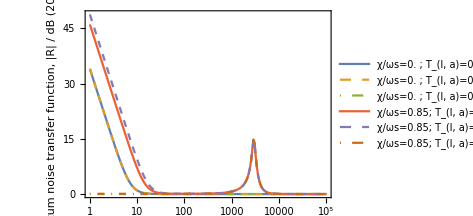
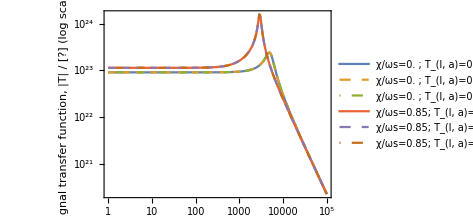
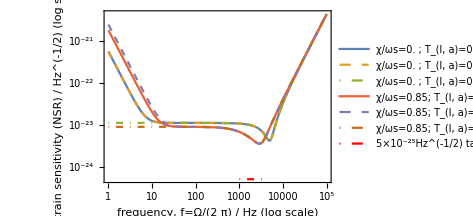

```mathematica
χRatio0=0.85;
valsList1={
{0,0.1,0.1,0.1,0.1},
{0,0.1,0.1,0.1,0.1,True,False,False},
{0,0.1,0.1,0.1,0.1,False,False,False},
{χRatio0 ωs,0.1,0.1,0.1,0.1},
{χRatio0 ωs,0.1,0.1,0.1,0.1,True,False,False},
{χRatio0 ωs,0.1,0.1,0.1,0.1,False,False,False}};
plotwRP[valsList1,None,{,Dashed,DotDashed}]
```

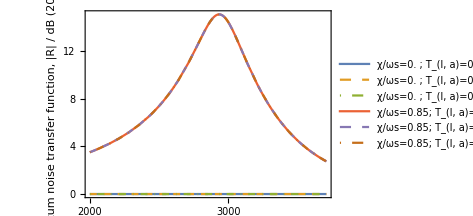
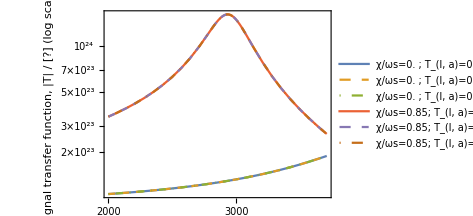
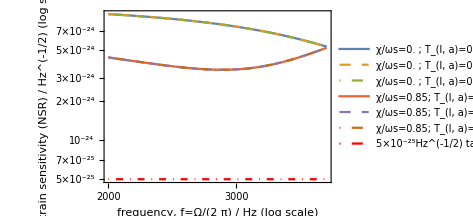

```mathematica
(*checking no double peak -- looks the same with PerformanceGoal->Quality
to-do: for completeness, should find all local maxima -- maybe part of threshold plots?*)
plotwRP[valsList1,None,{,Dashed,DotDashed},2 10^3,4 10^3]
```

```mathematica
(*NB: radiation pressure worsened because squeezing is in phase quadrature,
to-do: frequency dependent internal squeezing?*)
```

```mathematica
(*to-do: copy other plotting functions from sWLC:,
- stability --> not necessary, same denominator in transfer functions so same stability,
- noise budget --> done, but I don't know how to turn off shot noise? ,
- optimum sensitivity at probe frequency --> done, 2.5k is most interesting,
*)
```

```mathematica
(*noise budget,
to-do: turn shot noise off to plot radiation pressure separately, how?*)
RpdwRP[Ω0_,χ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=Re[Sqrt[(Rpd Id)[[2,2]]]]/.{
Ω->Ω0,χ->χ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
RinwRP[Ω0_,χ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=Re[Sqrt[(Rin.ConjugateTranspose[Rin])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
RawRP[Ω0_,χ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=Re[Sqrt[(Ra.ConjugateTranspose[Ra])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
RbwRP[Ω0_,χ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=Re[Sqrt[(Rb.ConjugateTranspose[Rb])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
RcwRP[Ω0_,χ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=Re[Sqrt[(Rc.ConjugateTranspose[Rc])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}

plotNoiseBudgetwRP[params_,fRange_:{1,10^5}]:=
LogLinearPlot[{
20Log10[1],
20Log10[RinwRP@@Join[{2π f},params]],
20Log10[RawRP@@Join[{2π f},params]],
20Log10[RbwRP@@Join[{2π f},params]],
20Log10[RcwRP@@Join[{2π f},params]],
20Log10[RpdwRP@@Join[{2π f},params]],
20Log10[QNwRP@@Join[{2π f},params]]},{f,fRange[[1]],fRange[[2]]},PlotLegends->LineLegend[{"vacuum","R_in, behind SRM","(R^(L))_a, arm intra-cav.","(R^(L))_b, SRC signal intra-cav.","(R^(L))_c, SRC idler intra-cav.","(R^(L))_PD, PD loss","total quantum noise"},LabelStyle->Directive[10],LegendLabel->legendStyler[params]],PlotRange->All,PlotStyle->{Directive[Gray,Dashed],,,,,,Directive[Black,Dashed]},Frame->True,FrameLabel->{{"quantum noise transfer function,\n|R| / dB (20log10)",},{"frequency, f=Ω/(2  π) / Hz","nondegenerate internal squeezing\nparameters of LIGO Voyager"}},PerformanceGoal->"Speed"]
```

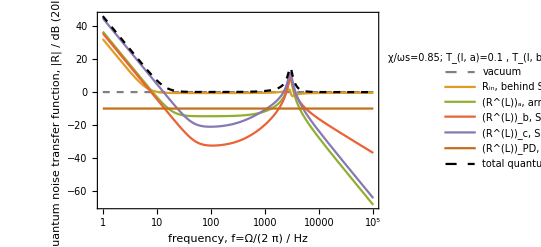

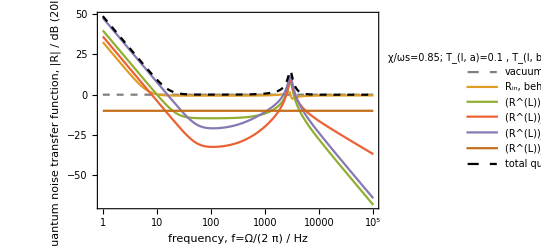

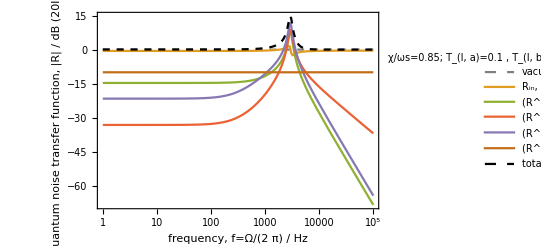

```mathematica
χRatio0=0.85;
plotNoiseBudgetwRP[{χRatio0 ωs,0.1,0.1,0.1,0.1}]
plotNoiseBudgetwRP[{χRatio0 ωs,0.1,0.1,0.1,0.1,True,False,False}]
plotNoiseBudgetwRP[{χRatio0 ωs,0.1,0.1,0.1,0.1,False,False,False}]
```

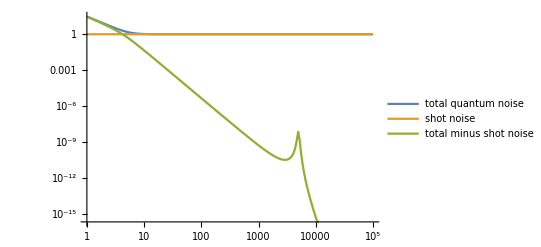

```mathematica
(*to-do: turn shot noise off (how?) to plot radiation pressure separately*)
LogLogPlot[{
QNwRP[2π f,0,0,0,0,0],
QNwRP[2π f,0,0,0,0,0,False,False,False],
QNwRP[2π f,0,0,0,0,0]-QNwRP[2π f,0,0,0,0,0,False,False,False]},
{f,1,10^5},PerformanceGoal->"Speed",PlotRange->All,PlotLegends->{"total quantum noise","shot noise","total minus shot noise"}]
```

```mathematica
(*optimum sensitivity at probe frequency*)
plotThresholdFinder[fProbe_,Tlc_,pastThreshold_:False,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=(
probeNoiseRef=QNwRP[2π fProbe,0,0,0,0,0,ρRPTrue,ρBAETrue,False];(*reference has no γc loss*)
probeSigRef=sigwRP[2π fProbe,0,0,0,0,0,ρRPTrue,ρBAETrue,False];
probeSensRef=ASDShwRP[2π fProbe,0,0,0,0,0,ρRPTrue,ρBAETrue,False];
rpdList=Subdivide[0,0.5,5];
p1=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[QNwRP[2π fProbe,χRatio ωs,0,0,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],-20Log10[ASDShwRP[2π fProbe,χRatio ωs,0,0,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeSensRef]}},{i,1,Length[rpdList]}],1]],{χRatio,0,1},Frame->True,FrameLabel->{{StringForm["SNR (Hz^(1/2)) gain at `` kHz\nrelative to no loss/sqz. / dB (20 log_10(1/S_h))",N[fProbe/10^3]],},{,"nondegenerate internal squeezing\nparameters of LIGO Voyager"}},PlotStyle->Table[Blend[{Blue,Green},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotLegends->LineLegend[{Table[StringForm["χ/ωs∈(0,1), R_PD=``",NumberForm[N[rpdList[[i]]]]],{i,1,Length[rpdList]}]},LabelStyle->Directive[10],LegendLabel->StringForm["T_(l, c)=``"<>If[Not[ρRPTrue],"; no RP",""]<>If[Not[ρBAETrue],"; no BAE",""],NumberForm[N[Tlc]]]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,AspectRatio->1,PerformanceGoal->"Speed"];
p2=ParametricPlot[{
{-20Log10[QNwRP[2π fProbe,1 ωs,0,0,Tlc,Rpd,ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],-20Log10[ASDShwRP[2π fProbe,1 ωs,0,0,Tlc,Rpd,ρRPTrue,ρBAETrue,symSRM]/probeSensRef]}},{Rpd,rpdList[[1]],rpdList[[-1]]},Frame->True,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{StringForm["χ/ωs=1, varying R_PD∈(``,``)",NumberForm[N[rpdList[[1]]]],NumberForm[N[rpdList[[-1]]]]]},LabelStyle->Directive[10]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,PerformanceGoal->"Speed"];
If[pastThreshold,
p1b=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[QNwRP[2π fProbe,χRatio ωs,0,0,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],-20Log10[ASDShwRP[2π fProbe,χRatio ωs,0,0,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeSensRef]}},{i,1,Length[rpdList]}],1]],{χRatio,1,2},Frame->True,PlotStyle->Table[Blend[{Red,Yellow},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotLegends->LineLegend[{Table[StringForm["χ/ωs∈(1,2), R_PD=``",NumberForm[N[rpdList[[i]]]]],{i,1,Length[rpdList]}]},LabelStyle->Directive[10]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,PerformanceGoal->"Speed"];
p1and2=Show[p1,p1b,p2];,
p1and2=Show[p1,p2];];
p3=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[QNwRP[2π fProbe,χRatio ωs,0,0,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],20Log10[sigwRP[2π fProbe,χRatio ωs,0,0,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeSigRef]}},{i,1,Length[rpdList]}],1]],{χRatio,0,1},Frame->True,FrameLabel->{{StringForm["signal transfer function |T| at `` kHz\nrelative to no loss/sqz. / dB (20 log_10)",N[fProbe/10^3]],},{StringForm["quantum noise transfer function |R| at `` kHz\nrelative to no loss/sqz. / dB (-20 log_10)",N[fProbe/10^3]],}},PlotStyle->Table[Blend[{Blue,Green},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotRange->All,ImagePadding->{{80,10},{All,1}},ImageSize->350,AspectRatio->3/4,PerformanceGoal->"Speed"];
p4=ParametricPlot[
{-20Log10[QNwRP[2π fProbe,1ωs,0,0,Tlc,Rpd,ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],
20Log10[sigwRP[2π fProbe,1ωs,0,0,Tlc,Rpd,ρRPTrue,ρBAETrue,symSRM]/probeSigRef]},{Rpd,rpdList[[1]],rpdList[[-1]]},Frame->True,PlotStyle->Directive[Black,Dashed],PlotRange->All,ImagePadding->{{80,10},{All,1}}];
If[pastThreshold,
p3b=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[QNwRP[2π fProbe,χRatio ωs,0,0,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],20Log10[sigwRP[2π fProbe,χRatio ωs,0,0,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeSigRef]}},{i,1,Length[rpdList]}],1]],{χRatio,1,2},Frame->True,PlotStyle->Table[Blend[{Red,Yellow},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,PerformanceGoal->"Speed"];
p3and4=Show[p3,p3b,p4];,
p3and4=Show[p3,p4];];
Column[{p1and2,p3and4},Spacings->0])
```

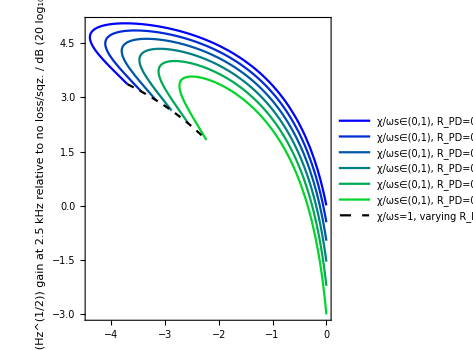
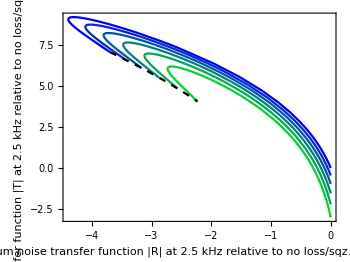

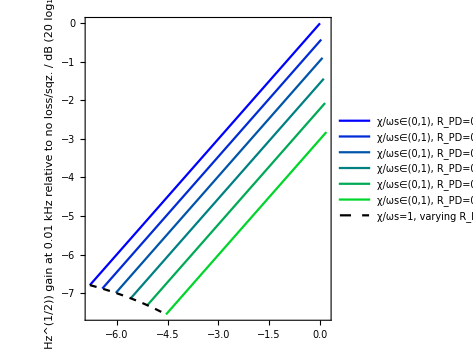
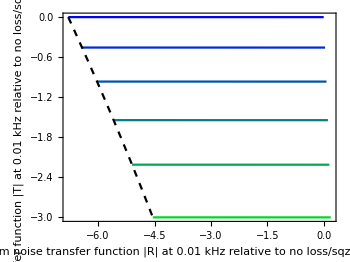

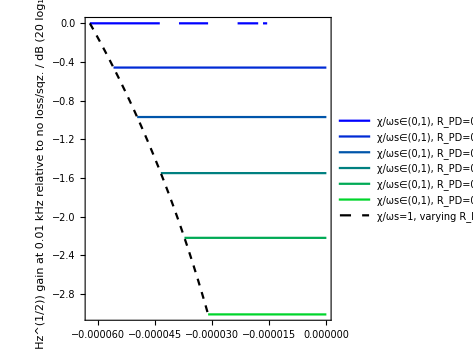
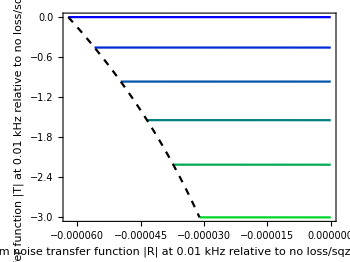

```mathematica
(*fProbe_,Tlc_,pastThreshold_:False,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False*)
plotThresholdFinder[2500(*Hz*),0.1]
plotThresholdFinder[10(*Hz*),0.1]
plotThresholdFinder[10(*Hz*),0.1,False,False,False]
```